## Exercise 2

In this section, we consider the Wigner spike model for spiked matrix estimation. The model assumes we are given data ,  a symmetric matrix defined as:
																				    
where:
-  is a random vector, representing the true signal,  with i.i.d. entries drawn from a prior distribution .
-  is symmetric i.i.d. noise with  for .
The posterior probability  can be written in the form of a Boltzmann Distribution, in particular , the dependence on Y, which in turns depends on the realization of the random variables: , identify a disordered system, where the key assumption would be that, in the Thermodynamic Limit (), the quantities of  are all self-averaging, namely they do not depend on the particular realization of the disorder random variables, but rather concentrate around the average over  the disorder.
As in all Statistical Physics problems, the fundamental task is to compute the Free entropy density: . This can be done introducing   independent copies of the system and relying in the Replica Method, with the so called replica trick:
																         
In the problem considered this allows to find an expression for the Free Entropy density, depending on the overlap with the truth:  and the signal to noise ratio (SNR.
)
															       where  
The equilibrium overlap  maximizes the previous expression. Imposing this condition one can obtain the following self-consistent equation:
																	
The importance of  in this context is its relation with the minimum square error, indeed can be shown that:     . 
The exercise ask to solve the self-consistent equation for a Gauss, Rademacher and Rademacher-Bernoulli random variables, and observe possible phase transition in the overlap varying SNR, where a transition from a zero to a non zero , means a theoretical prediction about a transition between a maximum MMSE to a decreasing one, going from a region in which is impossible to recover the signal to one in which is possible with a certain optimal MMSE.

In the PDF file the self-consistent equation is simplified consider the information provided by the prior under examination. The resulting expression are the one implemented in the cose.

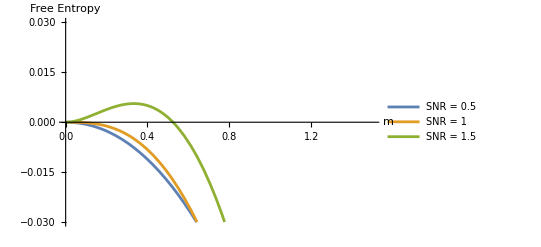

```mathematica
(*Free Energy plot*)
Frs[m_,SNR_]:=-SNR/4*m^2-1/2*Log[1+SNR*m]+SNR*m/2
Plot[{Frs[m,0.5],Frs[m,1],Frs[m,1.5]},{m,0,1.5},
PlotRange->{-0.03,0.03},
PlotLegends->{"SNR = 0.5","SNR = 1","SNR = 1.5"},
AxesLabel->{"m","Free Entropy"}]
```

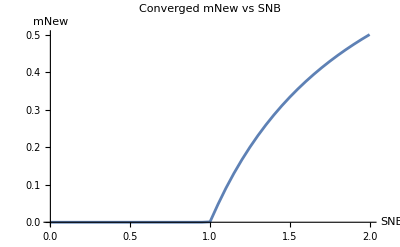

```mathematica
(*Self consistent overlap for a Gaussian Prior*)
results=Table[Module[{mNew=0.1,mOld=0,tolerance=10^-6},
While[Abs[mNew-mOld]>tolerance,mOld=mNew;
mNew=mOld*SNR/(1+SNR*mOld)];
{SNR,mNew}],
{SNR,0,2,0.05}];
ListLinePlot[results,AxesLabel->{"SNR","mNew"},PlotLabel->"Converged mNew vs SNR"]
```

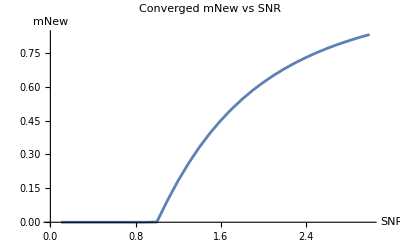

```mathematica
(*Self consistent overlap for a Rademacher Prior*)
SNR=1; (*Example value of SNR*)
mUpdate[m_,SNR_]:=NIntegrate[Exp[-z^2/2]/Sqrt[2*Pi]*Tanh[SNR*m+Sqrt[SNR*m]*z],{z,-5,5}];

results1=Table[Module[{mNew=0.1,mOld=0,tolerance=10^-6},
While[Abs[mNew-mOld]>tolerance,mOld=mNew;
mNew=mUpdate[mOld,SNR]];
{SNR,mNew}],
{SNR,0.1,3,0.1}];
ListLinePlot[results1,AxesLabel->{"SNR","mNew"},PlotLabel->"Converged mNew vs SNR"]
```

In the third case the prior gives with a probability     result 0 or a Rademacher random variable otherwise. The parameter   is also referred as sparsity, since when it increases the amount of null information increases. Starting from  = 1, one recover coherently the previous case, when sparsity increases, the critical signal to noise ratio increases too, meaning that we need a greater amount of signal for being able to recover it, in the meanwhile, when we are in the recovery phase, for the same SNR the maximum theoretically achievable overlap with the truth decrease with sparsity. 
For really high sparsity, like , one can see that there is an almost vertical transition, rather resembling a First Order Phase Transition, in this case the maximum overlap is almost negligible.

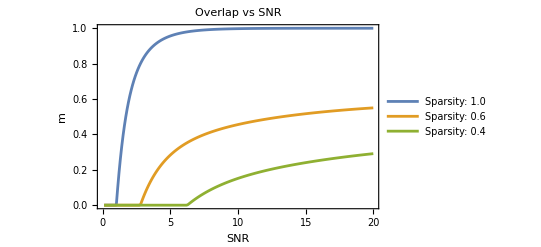

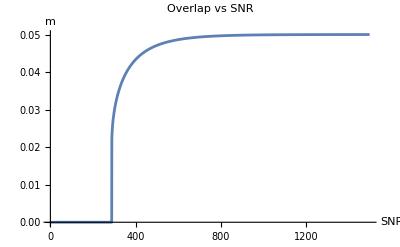

```mathematica
(*Self consistent overlap for a Rademacher Prior with sparsity*)
rho=0.7; (*Example value of rho*)
mUpdate2[m_,SNR_,rho_]:=NIntegrate[Exp[-z^2/2]/Sqrt[2*Pi]*rho^2  *Tanh[SNR*m+Sqrt[SNR*m]*z]/((1-rho)*Exp[SNR*m/2]/Cosh[SNR*m+Sqrt[SNR*m]*z]+rho  ),{z,-10,10}]
LowSpars=Table[Module[{mNew=0.1,mOld=0,tolerance=10^-6},
While[Abs[mNew-mOld]>tolerance,mOld=mNew;
mNew=mUpdate2[mOld,SNR,1]];
{SNR,mNew}],
{SNR,0.1,20,0.1}];
midSpars=Table[Module[{mNew=0.1,mOld=0,tolerance=10^-6},
While[Abs[mNew-mOld]>tolerance,mOld=mNew;
mNew=mUpdate2[mOld,SNR,0.6]];
{SNR,mNew}],
{SNR,0.1,20,0.1}];
highSpars=Table[Module[{mNew=0.1,mOld=0,tolerance=10^-6},
While[Abs[mNew-mOld]>tolerance,mOld=mNew;
mNew=mUpdate2[mOld,SNR,0.4]];
{SNR,mNew}],
{SNR,0.1,20,0.1}];
ListLinePlot[{LowSpars,midSpars,highSpars},PlotLegends->{"Sparsity: 1.0","Sparsity: 0.6","Sparsity: 0.4"},Frame->True,FrameLabel->{"SNR","m"},PlotRange->All,LabelStyle->Directive[Bold,14],PlotLabel->"Overlap vs SNR"]

highhighSpars=Table[Module[{mNew=0.1,mOld=0,tolerance=10^-6},
While[Abs[mNew-mOld]>tolerance,mOld=mNew;
mNew=mUpdate2[mOld,SNR,0.05]];
{SNR,mNew}],
{SNR,0.1,1500,0.5}];
ListLinePlot[highhighSpars,AxesLabel->{"SNR","m"},PlotLabel->"Overlap vs SNR",PlotRange->Full]
```